# Workshop 5-b : Hyperbolic Tangent Potential

Author:  Ángel Salazar

School of Physical Sciences and Nanotechnology

## Hypergeometric differential equation: Solution

First we define the quantities:

```mathematica
ν[En_] := (√((En+a)^2-m^2))/(2 b);
λ = (b+√(b^2-4 a^2))/(2 b);
μ[En_] :=(√((En-a)^2-m^2))/(2 b); 
μ1[En_]:=-μ[En];
```

The general solution in terms of variable x of the hypergeometric differential equations is:

```mathematica
ϕ[x_]:=c1 (-Exp[2 b x])^(ⅈ ν) (1+Exp[2 b x])^λ Hypergeometric2F1[ⅈ ν +λ -ⅈ μ, ⅈ ν + λ+ⅈ μ, 1 +2 ⅈ ν, -Exp[2b x]]+c2 (-Exp[2 b x])^(-ⅈ ν) (1+ Exp[2 b x]^λ) Hypergeometric2F1[-ⅈ ν+λ+ⅈ μ, -i ν+λ-ⅈ μ,1-2 ⅈ ν,-Exp[2 b x]]
```

Then the incident and reflected waves are:

```mathematica
Subscript[ϕ, inc][y_]:= A (1 + Exp[2 b x ]^λ )Exp[2 ⅈ b ν x] Hypergeometric2F1[ⅈ ν +λ-ⅈ μ, ⅈ ν + λ + ⅈ μ, 1 + 2 ⅈ ν, -Exp[2 b x]];
Subscript[ϕ, ref][y_]:= B (1 + Exp[2 b x ]^λ )Exp[-2 ⅈ b ν x] Hypergeometric2F1[-ⅈ ν +λ+ⅈ μ, -ⅈ ν + λ - ⅈ μ, 1 - 2 ⅈ ν, -Exp[2 b x]];
```

The transmitted wave is:

```mathematica
Subscript[ϕ, trans][x_]:=d3 Exp[-2 b λ x](1+Exp[2 b x])^λ Exp[2 ⅈ b μ x] Hypergeometric2F1[ⅈ ν + λ -ⅈ μ, -ⅈ ν + λ- ⅈ μ, 1-2 ⅈ μ, -Exp[-2 b x]];
```

The coefficient A and B can be expressed in terms of the Gamma function as:

```mathematica
A1[λ_,μ_,ν_]:=(Gamma[1-2 ⅈ μ] Gamma[-2 ⅈ ν])/(Gamma[-ⅈ ν +λ-ⅈ μ] Gamma[1 - ⅈ ν - λ -ⅈ μ]);
B1[λ_,μ_,ν_]:=(Gamma[1-2 ⅈ μ] Gamma[2 ⅈ ν])/(Gamma[ⅈ ν +λ-ⅈ μ] Gamma[1 + ⅈ ν - λ -ⅈ μ]);
```

Then the reflection R and transmission coefficient T are:

```mathematica
νp[En_]:=Sign[En+a] √Max[(En+a)^2-m^2,0]/(2 b);
μp[En_]:=Sign[En-a] √Max[(En-a)^2-m^2,0]/(2 b);
```

```mathematica
Rf[En_?NumericQ]:=Module[{A0,B0},A0=A1[λ,μ1[En],ν[En]];
B0=B1[λ,μ1[En],ν[En]];
N[Abs[B0]^2/Abs[A0]^2,40]];

Tf[En_?NumericQ]:=N[(μp[En]/νp[En])1/Abs[A1[λ,μ1[En],ν[En]]]^2,40];
```

```mathematica
(*a-m<En<a+m*)
Rf2[En_]:=1.;
Tf2[En_]:=0.;
```

```mathematica
Rf3[En_?NumericQ]:=Module[{A0,B0},A0=A1[λ,μ[En],ν[En]];
B0=B1[λ,μ[En],ν[En]];
N[Abs[B0]^2/Abs[A0]^2,40]];

Tf3[En_?NumericQ]:=N[(μp[En]/νp[En])1/Abs[A1[λ,μ[En],ν[En]]]^2,40];
```

```mathematica
eps=1.*^-2;
Rtot[En_?NumericQ]:=Piecewise[{{Rf[En],En<=a-m-eps},
{Rf2[En],a-m-eps<En<a+m+eps},
{Rf3[En],En>=a+m+eps}   }];
Ttot[En_?NumericQ]:=Piecewise[{{Tf[En],En<=a-m-eps},
{Tf2[En],a-m-eps<En<a+m+eps},
{Tf3[En],En>=a+m+eps}  }];
```

## Plot 1:

```mathematica
a=5;
b=2;
m=1;
```

#### Test region: E<a-m

```mathematica
testR=Rf[3.]
```

1.81061

```mathematica
testT=Tf[3.]
```

-0.810611

```mathematica
testR+testT
```

1.

#### Test region: a-m>E>-a+m

```mathematica
testR=Rf3[7.]
```

0.00653046

```mathematica
testT=Tf3[7.]
```

0.99347

```mathematica
testR+testT
```

1.

#### Reflection

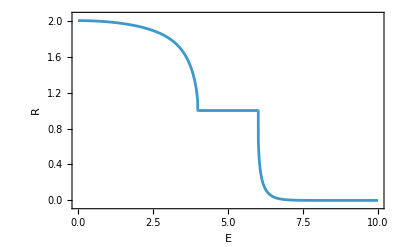

```mathematica
Plot[Rtot[En],{En,0,2 a},Exclusions->{a-m,a+m},ExclusionsStyle->None,PlotRange->{{0,2 a},{-0.05,2.05}},
Frame->True,
FrameLabel->{"E","R"}
]
```

#### Transmission

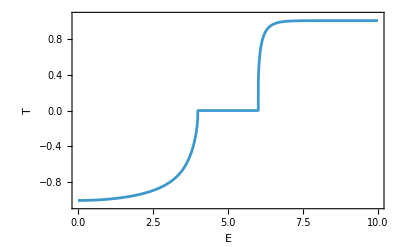

```mathematica
Plot[Ttot[En],{En,0,2 a},Exclusions->{a-m,a+m},ExclusionsStyle->None,PlotRange->{{0,2 a},{-1.05,1.05}},
Frame->True,
FrameLabel->{"E","T"}
]
```

## Plot 2:

```mathematica
Clear[a,b,m]
```

```mathematica
a=5;
b=50;
m=1;
```

#### Test region: E<a-m

```mathematica
testR=Rf[3.]
```

2.43477

```mathematica
testT=Tf[3.]
```

-1.43477

```mathematica
testR+testT
```

1.

#### Test region: a-m>E>-a+m

```mathematica
testR=Rf3[7.]
```

0.545424

```mathematica
testT=Tf3[7.]
```

0.454576

```mathematica
testR+testT
```

1.

#### Reflection

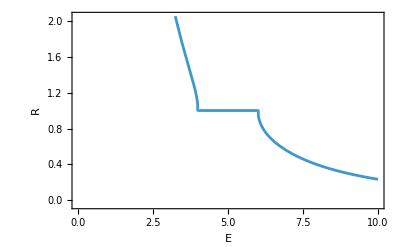

```mathematica
Plot[Rtot[En],{En,0,2 a},Exclusions->{a-m,a+m},ExclusionsStyle->None,PlotRange->{{0,2 a},{-0.05,2.05}},
Frame->True,
FrameLabel->{"E","R"}
]
```

#### Transmission

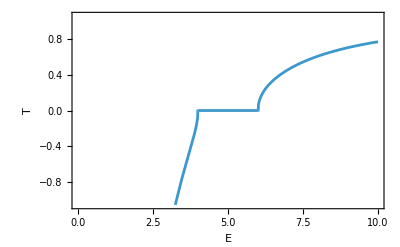

```mathematica
Plot[Ttot[En],{En,0,2 a},Exclusions->{a-m,a+m},ExclusionsStyle->None,PlotRange->{{0,2 a},{-1.05,1.05}},
Frame->True,
FrameLabel->{"E","T"}
]
```